## Converting Resistances to Temperatures

What I have done here is just read into Mathematica the tables for converting resistances to temperatures that appear in the lab manual.  From this, I have had Mathematica generate "interpolating functions" corrfunc[R/R300], which gives the temperature for the high temp lab, and corrfunc3[R], which gives the temperature for the low temp lab.  Both give temperatures in Kelvin (I converted the table for the low temp lab), the first takes as its input the ratio of resistance to room-temperature resistance, and the second takes the resistance directly.  I have plots below of the information in the table and the intepolating function, showing that it seems to work well.  I also then generated functions that were the derivatives of these, dcorrfunc and dcorrfunc3, for use in error propagation.

It is worth remembering that this process of interpolation falls apart if you try to use the resulting function outside of the range of values of the orginal table: so you shouldn't trust corrfunc outside of the range R/R300 = 1 to R/R300 = 19.66 (equivalent to the temperature range 300 K to 3500 K.)  Similarly, you shouldn't trust corrfunc3 outside the range R = 1331.9 ohms to R = 207850 ohms, (equivalent to temperature range 283 K to to 423 K.)

### High Temperature Lab

#### Entering the data table

```mathematica
correlation = {{1.00, 300}, {1.43, 400}, {1.87, 500}, {2.34, 600}, {2.85, 700}, {3.36, 800}, {3.88, 900}, {4.41, 1000}, {4.95, 1100}, {5.48, 1200}, {6.03, 1300}, {6.58, 1400}, {7.14, 1500}, {7.71, 1600}, {8.28, 1700}, {8.86, 1800}, {9.44, 1900}, {10.03, 2000}, {10.63, 2100}, {11.24, 2200}, {11.84, 2300}, {12.46, 2400}, {13.08, 2500}, {13.72, 2600}, {14.34, 2700}, {14.99, 2800}, {15.63, 2900}, {16.29, 3000}, {16.95, 3100}, {17.62, 3200}, {18.28, 3300}, {18.97, 3400}, {19.66, 3500}};
```

#### Creating the correlation function

```mathematica
corrfunc = Interpolation[correlation];
```

Here's my correlation function.

```mathematica
dcorrfunc[x_] := Evaluate[D[corrfunc[x], x]]
```

Here's its derivative

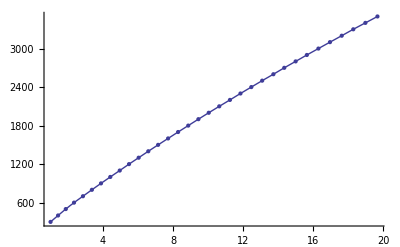

```mathematica
Show[{ListPlot[correlation], Plot[corrfunc[x], {x, 1, 19.66}]}]
```

And here's what it looks like when plotted.

### Low Temperature Lab

#### Entering the data table

```mathematica
correlation2  = {{207850, 10}, {197560, 11}, {187840, 12}, {178650, 13}, {169950, 14}, {161730, 15}, {153950, 16}, {146580, 17}, {139610, 18}, {133000, 19}, {126740, 20}, {120810, 21}, {115190, 22}, {109850, 23}, {104800, 24}, {100000, 25}, {95447, 26}, {91126, 27}, {87022, 28}, {83124, 29}, {79422, 30}, {75903, 31}, {72560, 32}, {69380, 33}, {66356, 34}, {63480, 35}, {60743, 36}, {58138, 37}, {55658, 38}, {53297, 39}, {51048, 40}, {48905, 41}, {46863, 42}, {44917, 43}, {43062, 44}, {41929, 45}, {39605, 46}, {37995, 47}, {36458, 48}, {34991, 49}, {33591, 50}, {32253, 51}, {30976, 52}, {29756, 53}, {28590, 54}, {27475, 55}, {26409, 56}, {25390, 57}, {24415, 58}, {23483, 59}, {22590, 60}, {21736, 61}, {20919, 62}, {20136, 63}, {19386, 64}, {18668, 65}, {17980, 66}, {17321, 67}, {16689, 68}, {16083, 69}, {15502, 70}, {14945, 71}, {14410, 72}, {13897, 73}, {13405, 74}, {12932, 75}, {12479, 76}, {12043, 77}, {11625, 78}, {11223, 79}, {10837, 80}, {10467, 81}, {10110, 82}, {9767.2, 83}, {9437.7, 84}, {9120.8, 85}, {8816.0, 86}, {8522.7, 87}, {8240.6, 88}, {7969.1, 89}, {7707.7, 90}, {7456.2, 91}, {7214.0, 92}, {6980.6, 93}, {6755.9, 94}, {6539.4, 95}, {6330.8, 96}, {6129.8, 97}, {5936.1, 98}, {5749.3, 99}, {5569.3, 100}, {5395.6, 101}, {5228.1, 102}, {5066.6, 103}, {4910.7, 104}, {4760.3, 105}, {4615.1, 106}, {4475.0, 107}, {4339.7, 108}, {4209.1, 109}, {4082.9, 110}, {3961.1, 111}, {3843.4, 112}, {3729.7, 113}, {3619.8, 114}, {3513.6, 115}, {3411.0, 116}, {3311.8, 117}, {3215.8, 118}, {3123.0, 119}, {3033.3, 120}, {2946.5, 121}, {2862.5, 122}, {2781.3, 123}, {2702.7, 124}, {2626.6, 125}, {2553.0,126}, {2481.7, 127}, {2412.6, 128}, {2345.8, 129}, {2281.0, 130}, {2218.3, 131}, {2157.6, 132}, {2098.7, 133}, {2041.7, 134}, {1986.4, 135}, {1932.8, 136}, {1880.9, 137}, {1830.5, 138}, {1781.7, 139}, {1734.3, 140}, {1688.4, 141}, {1643.9, 142}, {1600.6, 143}, {1558.7, 144}, {1518.0, 145}, {1478.6, 146}, {1440.2, 147}, {1403.0, 148}, {1366.9, 149}, {1331.9, 150}};
```

The original table gave temperatures in Celsius, so I convert here to Kelvin.

```mathematica
correlation3 = Table[{correlation2[[i,1]], correlation2[[i,2]] + 273.15}, {i, 1, Length[correlation2]}];
```

#### Creating the correlation function

```mathematica
corrfunc3 = Interpolation[correlation3];
```

Here's the correlation function

```mathematica
dcorrfunc3[x_] := Evaluate[D[corrfunc3[x], x]]
```

Here's its derivative

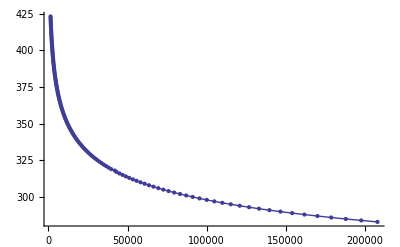

```mathematica
Show[{ListPlot[correlation3], Plot[corrfunc3[x], {x, 1332, 207850}]}]
```

And here's what it looks like when plotted.